## PolygonIntersection-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 20:51:39
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

```mathematica
polygon={{0.6656821861024209,0.5885139068629628},{0.3674265409089722,0.548792012192189},{-0.5083022778120968,0.03200749861905844},{-0.9625187848327785,-0.40634552703524995},{-0.603944818863048,-0.6296344493677282},{-0.2938861906733466,-0.19134629851828722},{0.3771323695082593,0.14124017268253336}};
direction={.5, -.3};
```

```mathematica
intersections=PolygonIntersection[direction, polygon]
```

{{2,{-0.362635,0.117968}},{6,{-0.0492218,-0.0700798}}}

```mathematica
edge2=polygon[[{2,3}]]
```

{{0.367427,0.548792},{-0.508302,0.0320075}}

```mathematica
edge6=polygon[[{6,7}]]
```

{{-0.293886,-0.191346},{0.377132,0.14124}}

```mathematica
point=Centroid[polygon]
```

{-0.178253,0.00733889}

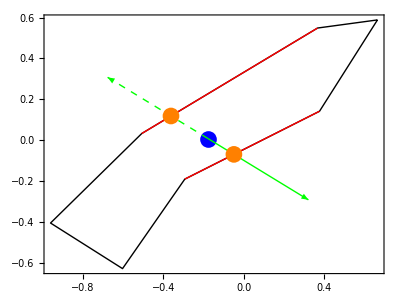

```mathematica
Show[Boundary[polygon],
Graphics[{Blue, PointSize[.03], Point[point], Red, Thick, Line[edge2], Line[edge6], Green, 
Arrow[{point, point+direction}], Dashed,
Arrow[{point, point -direction}], 
Orange, Point[intersections[[1,2]]], Point[intersections[[2,2]]]
}], 
 Frame-> True]
```